```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kthierbach/Documents/current/maria

```mathematica
dirs2i=FileNames["2i-pt*",{"./"}]
```

{./2i-pt-11,./2i-pt-12,./2i-pt-13,./2i-pt-14,./2i-pt-15,./2i-pt-16,./2i-pt-25,./2i-pt-26,./2i-pt-27,./2i-pt-28,./2i-pt-29,./2i-pt-30}

```mathematica
dirsLif=FileNames["lif-pt*",{"./"}]
```

{./lif-pt-01,./lif-pt-02,./lif-pt-03,./lif-pt-04,./lif-pt-05,./lif-pt-06,./lif-pt-07,./lif-pt-09,./lif-pt-10}

```mathematica
{color2i,colorLif}={Red,Blue};
```

```mathematica
SetOptions[ListLinePlot,{LabelStyle->{(FontFamily->"Helvetica"),(FontSize->14)},PlotStyle->Thickness[.02]}];
```

Global growth (2i = color2i, lif = colorLif)

```mathematica
bin2i=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirs2i);
binLif=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirsLif);
```

```mathematica
totalPixels=Length@Flatten@ImageData@Import[bin2i[[1,1]]]
```

262144

```mathematica
size2i=Map[Total@Flatten@ImageData@Import[#]/totalPixels&,bin2i,{2}];
sizeLif=Map[Total@Flatten@ImageData@Import[#]/totalPixels&,binLif,{2}];
```

```mathematica
meanSize2i=Mean@size2i;
meanSizeLif=Mean@sizeLif;
```

```mathematica
medianSize2i=Median@size2i;
medianSizeLif=Median@sizeLif;
```

```mathematica
stdSize2i=StandardDeviation@size2i;
stdSizeLif=StandardDeviation@sizeLif;
```

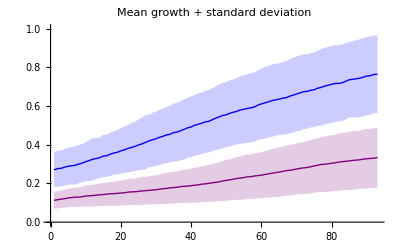

```mathematica
ListLinePlot[{meanSize2i,meanSize2i-stdSize2i,stdSize2i+meanSize2i,meanSizeLif,meanSizeLif-stdSizeLif,meanSizeLif+stdSizeLif},PlotStyle->{color2i,Opacity[0.],Opacity[0.],colorLif,Opacity[0.],Opacity[0.]},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotLabel->"Mean growth + standard deviation",PlotRange->{Automatic,{0,1}}]
```

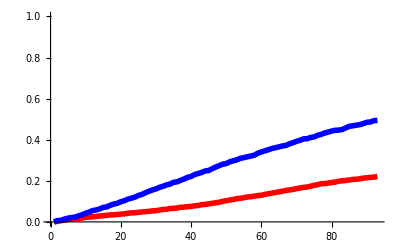

```mathematica
ListLinePlot[{meanSize2i-meanSize2i[[1]],meanSizeLif-meanSizeLif[[1]]},PlotStyle->{{Thickness[.01],color2i},{Thickness[0.01],colorLif}},PlotRange->{Automatic,{0,1}}]
```

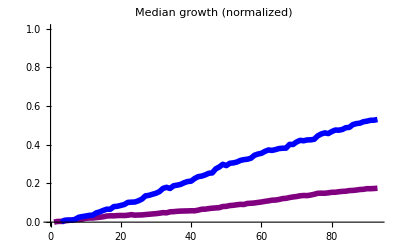

```mathematica
ListLinePlot[{medianSize2i-medianSize2i[[1]],medianSizeLif-medianSizeLif[[1]]},PlotStyle->{{Thickness[.01],color2i},{Thickness[0.01],colorLif}},PlotLabel->"Median growth (normalized)",PlotRange->{Automatic,{0,1}}]
```

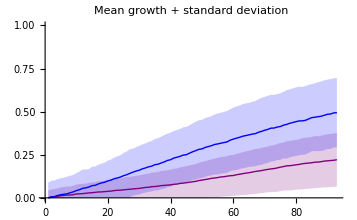

```mathematica
ListLinePlot[{meanSize2i-meanSize2i[[1]],meanSize2i-stdSize2i-meanSize2i[[1]],stdSize2i+meanSize2i-meanSize2i[[1]],meanSizeLif-meanSizeLif[[1]],meanSizeLif-stdSizeLif-meanSizeLif[[1]],meanSizeLif+stdSizeLif-meanSizeLif[[1]]},PlotStyle->{color2i,Opacity[0.],Opacity[0.],colorLif,Opacity[0.],Opacity[0.]},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotLabel->"Mean growth + standard deviation",PlotRange->{Automatic,{0,1}}]
```

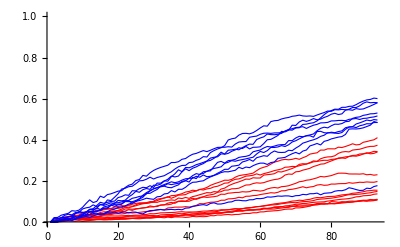

```mathematica
Show[ListLinePlot[#-First@#&/@size2i,PlotStyle->{{Thickness[0.002],color2i}}],ListLinePlot[#-First@#&/@sizeLif,PlotStyle->{{Thickness[0.002],colorLif}}],PlotRange->{Automatic,{0,1}}]
```

Der LIF Ausreisser ist lif-pt-07! Kleine Objecte habe ich bei der Berechnung nicht herausgeschmissen, da sie auch nicht wirklich einen Unterschied machen sollten.

Elongation (2i = color2i, lif = colorLif)

Hier entferne ich die kleinen Objekte <30 pixel. Ich habe einfach alle 2i frames und alle LIF frames zusammengeworfen, das muesste man nochmal diskutieren!? Die Formel im Paper ist auch falsch da muss stehen elongation = 1-λ_2/λ_1!

```mathematica
bin2i=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirs2i);
binLif=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirsLif);
```

```mathematica
elongation2i=Map[1-Divide@@Reverse@Last@#&,Map[ComponentMeasurements[DeleteSmallComponents[Import@#,30],"SemiAxes"]&,bin2i,{2}],{3}];
elongationLif=Map[1-Divide@@Reverse@Last@#&,Map[ComponentMeasurements[DeleteSmallComponents[Import@#,30],"SemiAxes"]&,binLif,{2}],{3}];
```

```mathematica
meanElongation2i=Mean/@(Flatten/@Transpose[elongation2i]);
meanElongationLif=Mean/@(Flatten/@Transpose[elongationLif]);
```

```mathematica
medianElongation2i=Median/@(Flatten/@Transpose[elongation2i]);
medianElongationLif=Median/@(Flatten/@Transpose[elongationLif]);
```

```mathematica
quantilesElongation2i=Transpose[Quantile[#,{.25,.75}]&/@(Flatten/@Transpose[elongation2i])];
quantilesElongationLif=Transpose[Quantile[#,{.25,.75}]&/@(Flatten/@Transpose[elongationLif])];
```

```mathematica
stdElongation2i=StandardDeviation/@(Flatten/@Transpose[elongation2i]);
stdElongationLif=StandardDeviation/@(Flatten/@Transpose[elongationLif]);
```

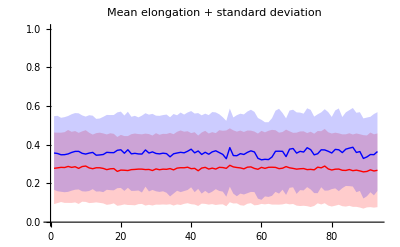

```mathematica
ListLinePlot[{meanElongation2i,meanElongation2i-stdElongation2i,meanElongation2i+stdElongation2i,meanElongationLif,meanElongationLif-stdElongationLif,meanElongationLif+stdElongationLif},PlotStyle->{color2i,Opacity[0.],Opacity[0.],colorLif,Opacity[0.],Opacity[0.]},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotLabel->"Mean elongation + standard deviation",PlotRange->{Automatic,{0,1}}]
```

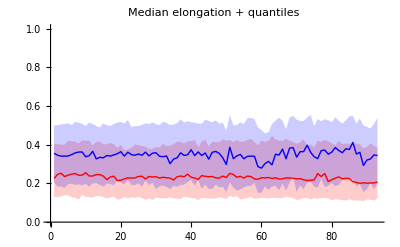

```mathematica
ListLinePlot[{medianElongation2i,quantilesElongation2i[[1]],quantilesElongation2i[[2]],medianElongationLif,quantilesElongationLif[[1]],quantilesElongationLif[[2]]},PlotStyle->{color2i,Opacity[0.],Opacity[0.],colorLif,Opacity[0.],Opacity[0.]},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotLabel->"Median elongation + quantiles",PlotRange->{Automatic,{0,1}}]
```

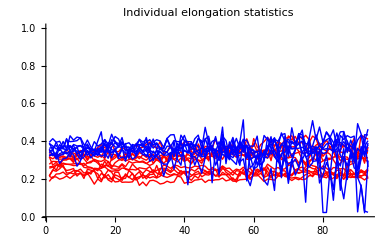

```mathematica
Show[ListLinePlot[Map[Mean,elongation2i,{2}],PlotStyle->{color2i}],ListLinePlot[Map[Mean,elongationLif,{2}],PlotStyle->{colorLif}],PlotLabel->"Individual elongation statistics",PlotRange->{Automatic,{0,1}}]
```

```mathematica
Manipulate[ListLinePlot[{Map[Mean,elongation2i[[i]]],Map[Mean,elongationLif[[j]]]},PlotStyle->{color2i,colorLif},PlotRange->{Automatic,{0,1}}],{i,1,Length@elongation2i,1},{j,1,Length@elongationLif,1}]
```

```mathematica
bla=MapIndexed[{First@#2,#1}&,Flatten/@Transpose@elongation2i,{2}];
ListPlot[Flatten[bla,{1,2}]]
```

Circularity (2i = color2i, lif = colorLif)

Hier entferne ich die kleinen Objekte <30 pixel. Ich habe einfach alle 2i frames und alle LIF frames zusammengeworfen, das muesste man nochmal diskutieren!?

```mathematica
bin2i=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirs2i);
binLif=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirsLif);
```

```mathematica
Manipulate[DeleteBorderComponents@DeleteSmallComponents[Import@binLif[[i,j]],50],{i,1,First@Dimensions@bin2i,1},{j,1,Last@Dimensions@bin2i,1}]
```

```mathematica
circularity2i=Map[Last@#&,ParallelMap[ComponentMeasurements[DeleteSmallComponents[Import@#,30],"FilledCircularity"]&,bin2i,{2}],{3}];
circularityLif=Map[Last@#&,ParallelMap[ComponentMeasurements[DeleteSmallComponents[Import@#,30],"FilledCircularity"]&,binLif,{2}],{3}];
```

```mathematica
meanCircularity2i=Map[Mean,circularity2i,{2}];
meanCircularityLif=Map[Mean,circularityLif,{2}];
```

```mathematica
stdOfMeanCircularity2i=StandardDeviation@meanCircularity2i;
stdOfMeanCircularityLif=StandardDeviation@meanCircularityLif;
```

```mathematica
meanCircularity2i=Mean/@(Flatten/@Transpose[circularity2i]);
meanCircularityLif=Mean/@(Flatten/@Transpose[circularityLif]);
```

```mathematica
stdCircularity2i=StandardDeviation/@(Flatten/@Transpose[circularity2i]);
stdCircularityLif=StandardDeviation/@(Flatten/@Transpose[circularityLif]);
```

```mathematica
medianCircularity2i=Median/@(Flatten/@Transpose[circularity2i]);
medianCircularityLif=Median/@(Flatten/@Transpose[circularityLif]);
```

```mathematica
quantilesCircularity2i=Transpose[Quantile[#,{.25,.75}]&/@(Flatten/@Transpose[circularity2i])];
quantilesCircularityLif=Transpose[Quantile[#,{.25,.75}]&/@(Flatten/@Transpose[circularityLif])];
```

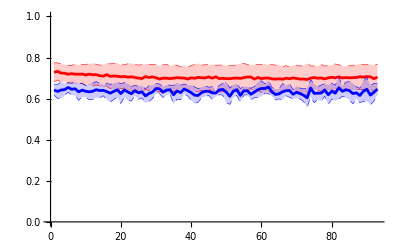

```mathematica
ListLinePlot[{Mean@meanCircularity2i,Mean@meanCircularity2i-stdOfMeanCircularity2i,Mean@meanCircularity2i+stdOfMeanCircularity2i,Mean@meanCircularityLif,Mean@meanCircularityLif-stdOfMeanCircularityLif,Mean@meanCircularityLif+stdOfMeanCircularityLif},PlotStyle->{{Thickness[.005],color2i},{color2i,Dashed,Thickness[.001]},{color2i,Dashed,Thickness[.001]},{Thickness[.005],colorLif},{colorLif,Dashed,Thickness[.001]},{colorLif,Dashed,Thickness[.001]}},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotRange->{Automatic,{0,1}}]
```

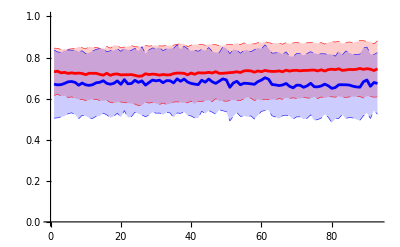

```mathematica
ListLinePlot[{meanCircularity2i,meanCircularity2i-stdCircularity2i,meanCircularity2i+stdCircularity2i,meanCircularityLif,meanCircularityLif-stdCircularityLif,meanCircularityLif+stdCircularityLif},PlotStyle->{{Thickness[.005],color2i},{color2i,Dashed,Thickness[.001]},{color2i,Dashed,Thickness[.001]},{Thickness[.005],colorLif},{colorLif,Dashed,Thickness[.001]},{colorLif,Dashed,Thickness[.001]}},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotRange->{Automatic,{0,1}}]
```

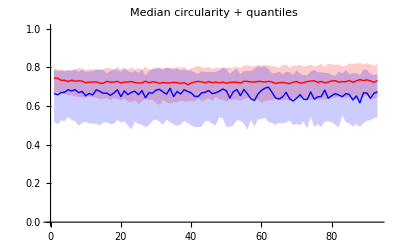

```mathematica
ListLinePlot[{medianCircularity2i,quantilesCircularity2i[[1]],quantilesCircularity2i[[2]],medianCircularityLif,quantilesCircularityLif[[1]],quantilesCircularityLif[[2]]},PlotStyle->{color2i,Opacity[0.],Opacity[0.],colorLif,Opacity[0.],Opacity[0.]},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotLabel->"Median circularity + quantiles",PlotRange->{Automatic,{0,1}}]
```

```mathematica
Manipulate[ListLinePlot[{Map[Mean,circularityLif[[j]]]},PlotStyle->{color2i,colorLif},PlotRange->{Automatic,{0,1}}],{i,1,Length@circularity2i,1},{j,1,Length@circularityLif,1}]
```

```mathematica
Show[ListLinePlot[Map[Mean,circularity2i,{2}],PlotStyle->{{Thickness[0.002],color2i}},PlotRange->{Automatic,{0,1}}],ListLinePlot[Map[Mean,circularityLif,{2}],PlotStyle->{{Thickness[0.002],colorLif}},PlotRange->{Automatic,{0,1}}]]
```

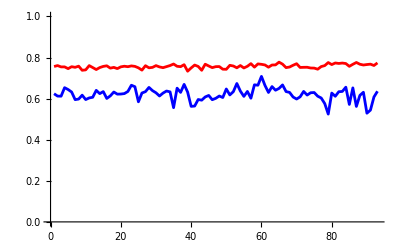

```mathematica
Show[ListLinePlot[Map[Mean,circularity2i,{2}][[1]],PlotStyle->{{Thickness[0.005],color2i}},PlotRange->{Automatic,{0,1}}],ListLinePlot[Map[Mean,circularityLif,{2}][[1]],PlotStyle->{{Thickness[0.005],colorLif}},PlotRange->{Automatic,{0,1}}],LabelStyle->{(FontFamily->"Helvetica"),(FontSize->14)}]
```

Entropy (2i = color2i, lif = colorLif)

Hier entferne ich die kleinen Objekte < 30 pixel. Ich habe einfach alle 2 i frames und alle LIF frames zusammengeworfen, das muesste man nochmal diskutieren!?

```mathematica
bin2i=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirs2i);
binLif=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirsLif);
```

```mathematica
images2i=Reverse/@(FileNames["*.tif",{#<>"/sz"}]&/@dirs2i);
imagesLif=Reverse/@(FileNames["*.tif",{#<>"/sz"}]&/@dirsLif);
```

```mathematica
entropy2i=Map[N@Last@#&,MapThread[ComponentMeasurements[{MorphologicalComponents@DeleteSmallComponents@Import@#1,Import@#2},"Entropy"]&,{bin2i,images2i},2],{3}];
entropyLif=Map[N@Last@#&,MapThread[ComponentMeasurements[{MorphologicalComponents@DeleteSmallComponents@Import@#1,Import@#2},"Entropy"]&,{binLif,imagesLif},2],{3}];
```

```mathematica
meanEntropy2i=Mean/@(Flatten/@Transpose[entropy2i]);
meanEntropyLif=Mean/@(Flatten/@Transpose[entropyLif]);
```

```mathematica
stdEntropy2i=StandardDeviation/@(Flatten/@Transpose[entropy2i]);
stdEntropyLif=StandardDeviation/@(Flatten/@Transpose[entropyLif]);
```

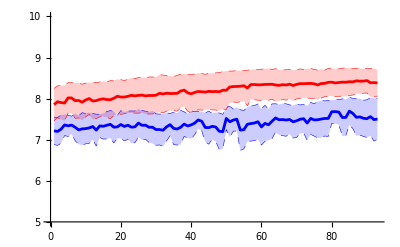

```mathematica
ListLinePlot[{meanEntropy2i,meanEntropy2i-stdEntropy2i,meanEntropy2i+stdEntropy2i,meanEntropyLif,meanEntropyLif-stdEntropyLif,meanEntropyLif+stdEntropyLif},PlotStyle->{{Thickness[.005],color2i},{color2i,Dashed,Thickness[.001]},{color2i,Dashed,Thickness[.001]},{Thickness[.005],colorLif},{colorLif,Dashed,Thickness[.001]},{colorLif,Dashed,Thickness[.001]}},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotRange->{Automatic,{5,10}}]
```

```mathematica
meanEntropy2i=Map[Mean,entropy2i,{2}];
meanEntropyLif=Map[Mean,entropyLif,{2}];
```

```mathematica
stdEntropy2i=StandardDeviation@meanEntropy2i;
stdEntropyLif=StandardDeviation@meanEntropyLif;
```

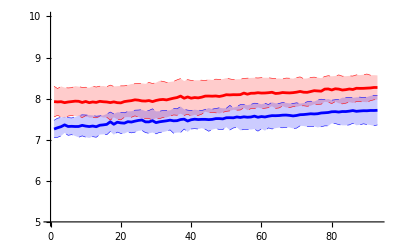

```mathematica
ListLinePlot[{Mean@meanEntropy2i,Mean@meanEntropy2i-stdEntropy2i,Mean@meanEntropy2i+stdEntropy2i,Mean@meanEntropyLif,Mean@meanEntropyLif-stdEntropyLif,Mean@meanEntropyLif+stdEntropyLif},PlotStyle->{{Thickness[.005],color2i},{color2i,Dashed,Thickness[.001]},{color2i,Dashed,Thickness[.001]},{Thickness[.005],colorLif},{colorLif,Dashed,Thickness[.001]},{colorLif,Dashed,Thickness[.001]}},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotRange->{Automatic,{5,10}}]
```

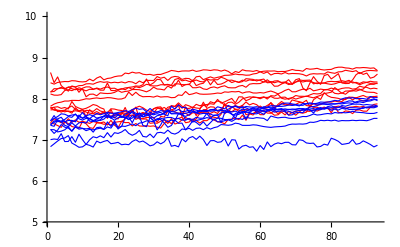

```mathematica
Show[{ListLinePlot[Map[Mean,entropy2i,{2}],PlotStyle->{{Thickness[0.002],color2i}}],ListLinePlot[Map[Mean,entropyLif,{2}],PlotStyle->{{Thickness[0.002],colorLif}}]},PlotRange->{Automatic,{5,10}},AxesOrigin->{0,5}]
```

Movement (2 i = color2i, lif = colorLif)

Figure 2 e), caption ist falsch geschrieben!

```mathematica
<<Eidomatica`
```

opencv::nolink: Can't find "opencv". Some functions may not work.

Revisions: {Eidomatica Package: 135, libEidomatica: 11}

```mathematica
bin2i=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirs2i);
binLif=Reverse/@(FileNames["*.png",{#<>"/bin"}]&/@dirsLif);
```

```mathematica
flows2i=Reverse/@(FileNames["*.dat",{#<>"/flows"}]&/@dirs2i);
flowsLif=Reverse/@(FileNames["*.dat",{#<>"/flows"}]&/@dirsLif);
```

```mathematica
Clear[pickVectors];
pickVectors[masks_,vectorField_]:=Pick[Flatten[vectorField,{1,2}],Flatten@#,1]&/@masks
```

```mathematica
norm2i=MapThread[Norm/@pickVectors[Last/@ComponentMeasurements[DeleteSmallComponents[Import[#1],30],"Mask"],eVectorFieldData@eBinaryImport[#2]]&,{Drop[#,1]&/@bin2i,flows2i},2]
normLif=MapThread[Norm/@pickVectors[Last/@ComponentMeasurements[DeleteSmallComponents[Import[#1],30],"Mask"],eBinaryImport[#2]]&,{Drop[#,1]&/@binLif,flowsLif},2]
```

```mathematica
{norm2i,normLif}={Import["norm2i.m"],Import["normLif.m"]};
```

```mathematica
meanDisplacement2i=Mean/@(Flatten/@Transpose[norm2i]);
meanDisplacementLif=Mean/@(Flatten/@Transpose[normLif]);
```

```mathematica
stdDisplacement2i=StandardDeviation/@(Flatten/@Transpose[norm2i]);
stdDisplacementLif=StandardDeviation/@(Flatten/@Transpose[normLif]);
```

```mathematica
medianDisplacement2i=Median/@(Flatten/@Transpose[norm2i]);
medianDisplacementLif=Median/@(Flatten/@Transpose[normLif]);
```

```mathematica
quantilesDisplacement2i=Transpose[Quantile[#,{.25,.75}]&/@(Flatten/@Transpose[norm2i])];
quantilesDisplacementLif=Transpose[Quantile[#,{.25,.75}]&/@(Flatten/@Transpose[normLif])];
```

```mathematica
meanDisplacement2i=Map[Mean,norm2i,{2}];
meanDisplacementLif=Map[Mean,normLif,{2}];
```

```mathematica
stdOfMeanDisplacement2i=StandardDeviation@meanDisplacement2i;
stdOfMeanDisplacementLif=StandardDeviation@meanDisplacementLif;
```

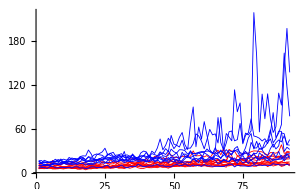

```mathematica
Show[ListLinePlot[meanDisplacement2i,PlotStyle->{{Thickness[.002],color2i}},PlotRange->All],ListLinePlot[meanDisplacementLif,PlotStyle->{{Thickness[.002],colorLif}},PlotRange->All]]
```

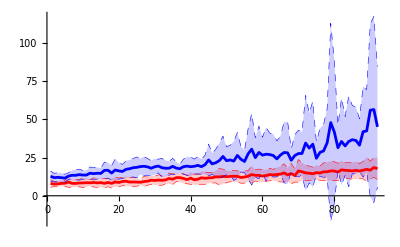

```mathematica
ListLinePlot[{Mean@meanDisplacement2i,Mean@meanDisplacement2i-stdOfMeanDisplacement2i,Mean@meanDisplacement2i+stdOfMeanDisplacement2i,Mean@meanDisplacementLif,Mean@meanDisplacementLif-stdOfMeanDisplacementLif,Mean@meanDisplacementLif+stdOfMeanDisplacementLif},PlotStyle->{{Thickness[.005],color2i},{color2i,Dashed,Thickness[.001]},{color2i,Dashed,Thickness[.001]},{Thickness[.005],colorLif},{colorLif,Dashed,Thickness[.001]},{colorLif,Dashed,Thickness[.001]}},Filling->{1->{{2},Directive[{color2i,Opacity[.2]}]},1->{{3},Directive[{color2i,Opacity[.2]}]},4->{{5},Directive[{colorLif,Opacity[.2]}]},4->{{6},Directive[{colorLif,Opacity[.2]}]}},PlotRange->All]
```

Tracking colony size

```mathematica
label2i=Reverse/@(FileNames["*.mat",{#<>"/label"}]&/@dirs2i);
labelLif=Reverse/@(FileNames["*.mat",{#<>"/label"}]&/@dirsLif);
```

```mathematica
divisions2i=Import[#<>"/divisions.m"]&/@dirs2i;
divisionsLif=Import[#<>"/divisions.m"]&/@dirsLif;
```

```mathematica
Clear[findTimePoint]
findTimePoint[divisions_,movie_]:=Block[
{ids,f},
ids=Map[Union@Flatten@IntegerPart@First@Import@#&,movie];
f[time_,list_]:={time,#}&/@list;
Flatten[Map[f[First@First@Position[ids,First@First@#],#]&,divisions],{1,2}]
]
```

```mathematica
divs2i=Map[findTimePoint[GatherBy[Flatten@#1,First],label2i[[First@#2]]]&,divisions2i];
divsLif=MapIndexed[findTimePoint[GatherBy[Flatten@#1,First],labelLif[[First@#2]]]&,divisionsLif];
```

```mathematica
measurements2i=Map[ComponentMeasurements[IntegerPart@First@Import@#,{"Count","Circularity"}]&,label2i,{2}];
measurementsLif=Map[ComponentMeasurements[IntegerPart@First@Import@#,{"Count","Circularity"}]&,labelLif,{2}];
```

```mathematica
Export["data.m",{"Divisions2i"->divs2i,"DivisionsLif"->divsLif,"Measurements2i"->measurements2i,"MeasurementsLif"->measurementsLif},"Comments"->"Measurements contain Count and Circularity"]
```

data.m